```mathematica
Clear[μ,B]
μ=5;
a=90*B;
Y[x_]:=(4*x^4)/a+x^2((a^2-4*x^4)/a^2)*Log[Abs[(2*x^2+a)/(2*x^2-a)]]
A[B_ ]:=NIntegrate[(Y[x])1/4 1/Cosh[(x-μ)/2]^2,{x,-50,50}]
```

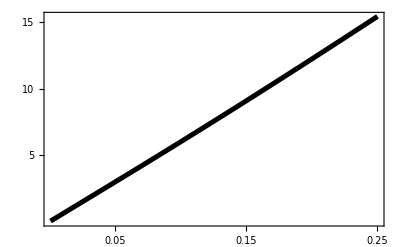

```mathematica
X1=Plot[{A[B]},{B,0.001,0.25},PlotStyle->{Black,Thickness[0.009]},ImagePadding->30,BaseStyle->{FontFamily->"Times",FontSize->16},Frame->{True,True,False,False},FrameStyle->Black,FrameTicks->{{0.05,0.15,0.25},{5,10,15}}]
```

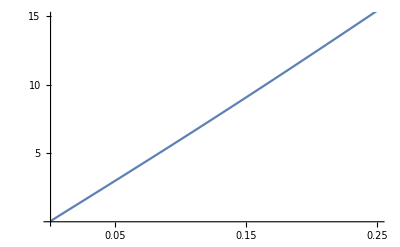

```mathematica
Show[%6,BaseStyle->{FontFamily->"Times",FontSize->20},PlotRange->{{0.001,.25},{0,15}},AxesOrigin->{0.001,0.01},Ticks->{{0.05,0.15,0.25},{5,10,15}}]
```

```mathematica
p=90*√B;
Y2[y_]:=(2 p x^2 y (2 p^2-4 x^4+p x^2 y)+(p^2-4 x^4)^2 Log[Abs[2 x^2+p y]])/p^3
A2[B_ ]:=NIntegrate[(Y2[1]-Y2[-1])1/4 1/Cosh[(x-μ)/2]^2,{x,-10,20}]
```

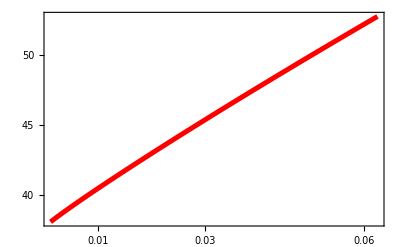

```mathematica
X2=Plot[{A2[B]},{B,0.001,0.0625},ImagePadding->30,BaseStyle->{FontFamily->"Times",FontSize->16},PlotStyle->{Red,Thickness[0.009]},Frame->{False,False,True,True},FrameStyle->Red,FrameTicks->{{0.01,0.03,0.06},{40,45,50}}]
```

```mathematica
,Axes->{False,False,False,True},Ticks->{None,None,None,All}
```

```mathematica
Overlay[{X1,X2}]
```

-Graphics--Graphics-

```mathematica
G1=Plot[x,{x,0,10},ImagePadding->20,PlotStyle->Red,Frame->{False,False,True,True},FrameStyle->Red,FrameTicks->{{2,5,7,9},{2,5,7,9}}];
G2=Plot[x^3,{x,0,10},ImagePadding->20,PlotStyle->Black,Frame->{True,True,False,False},FrameTicks->{All,All,None,None}];
```

```mathematica
Overlay[{X1,X2}]
```

-Graphics--Graphics-